#### puttana la madonna

```mathematica
Osservazione: si puó automatizzare la ricerca della biforcazione.
Per determinare la biforcazione n-esima si parte da un appropriato valore di μ inferiore a quello di boforcazione (stimato ad occhio) e si confrontano, per un opportunamente grande N, le iterate N-esima e (N+2^n)-esima di uno stesso punto inziale. Se sono molto vicini non siamo ancora alla biforcazione, e bisogna aumentare μ. Appena cominciano ad allontanarsi siamo arrivati alla biforcazione.
```

```mathematica
f[μ_,x_]:= μ x(1-x)
fn[μ_,x_,n_]:=Nest[f[μ,#]&,x,n]
check[x0_,μ_,nstart_]:= Mean[Differences[fn[x0,μ,nstart+2^#]&/@Range[5]]]
```

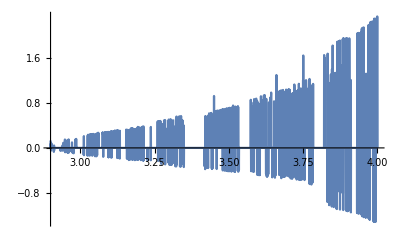

```mathematica
Plot[10^6 check[1/x,x,10]==0,{x,2.9,4}]
```

i primi 6 punti sono ben visibili, sono la fine delle parti “piatte”
possiamo vedere tutte le “zone piatte” più larghe di un tot, dove “un tot” è circa 1/3di tick, ci sono 4 tick tra 3.0 e 3.2  1 tick è 0.005. la zona che a noi interessa è circa larga 0.005/3 ossia 0.00166667 (≈16*10^-4)
il nostro sampling è 10^-5 ergo cerchiamo le zone piatte più larghe di 150 tick

```mathematica
data = Cases[Flatten[Table[{#⟦j⟧⟦1⟧,∑_(i=1)^150 #⟦i⟧⟦2⟧},{j,1,150}]&/@Partition[ParallelTable[{μ,Chop[10^6 check[1/μ,μ,10]]},{μ,2.9,4,10^-5}],150],1],{_,0.}]
```

{}

```mathematica
First/@candidatepoints
```

{2.9,3.4092}

```mathematica
Last/@candidatepoints
```

{3.40919,3.99949}

```mathematica
SequencePosition[data,Table[{_,0},150],Overlaps->False]
```

```mathematica
data0= ParallelTable[{μ,Chop[10^6 check[1/μ,μ,10]]},{μ,2.8,4,10^-5}];
```

{{2.8,0.0345763},{2.80001,0},{2.80002,0},{2.80003,0.0511488},{2.80004,-0.0511479},{2.80005,0},119990,{3.99996,0},{3.99997,0},{3.99998,-1.33103},{3.99999,0},{4.,0}}
 |  |  |  |

Partiziono la lista in liste più piccole così da poterci andare preciso.
la prima è da 2.8 a 3.2 circa
la lista è lunga

```mathematica
Length[data0]
```

120001

e va da 2.8 a 4 (lunga 1.2) ergo ogni .1 corrisponde a 10.000 tick
il primo scaglione è 2.8->3.2, il secondo 3.2->3.55, il terzo 3.55->3.65, il quarto 3.65->3.7 e butto il resto nel quinto.
ergo traducendo il primo è lungo 0.4, il secondo 0.35, il terzo 0.1, il quarto 0.05
ergo 40.000 tick, 35000, 10000,5000

```mathematica
manualseparate[list_,seps_]:= Take[list,#]&/@({seps[[#]]+1,seps[[#+1]]}&/@Range[Length[seps]-1])
```

```mathematica
datatot=manualseparate[data0,{0,4,7.5,8.5,9,12}10^4];
```

```mathematica
positions=Flatten[SequencePosition[datatot⟦#⟧,Table[{_,0},25-2#],Overlaps->False]&/@Range[Length[datatot]],1];
```

```mathematica
positions1 =First/@(First/@datatot⟦#⟧&/@positions)
```

{3.03253,2.80097,2.84659,2.85375,2.88302,2.92088,2.92128,2.92556,2.97998,3.04085,3.05545,2.80911,2.81361,2.8307,2.85857,2.87753,2.90003,2.90902,2.91656,2.94398,2.98812,3.00257,3.0211,3.05923,3.09549}

```mathematica
Map
```

```mathematica
ddata[x_]:=datatot⟦x⟧⟦#⟧&/@SequencePosition[datatot⟦x⟧,Table[{_,0},25-2x],Overlaps->False]
```

```mathematica
positions2=First/@(First/@Flatten[ddata[#]&/@Range[Length[datatot]],1])
```

{3.03253,3.20097,3.24659,3.25375,3.28302,3.32088,3.32128,3.32556,3.37998,3.44085,3.45545,3.55911,3.56361,3.6807,3.75857,3.77753,3.80003,3.80902,3.81656,3.84398,3.88812,3.90257,3.9211,3.95923,3.99549}

```mathematica
attrattivoPlot[nx_,n_,η_]:=With[{f=Compile[{{μ,_Real},{x,_Real}},μ x(1.-x)]},
ListPlot[
Union@Flatten[Table[
ParallelTable[
{μ,FixedPoint[Chop[f[μ,#]]&,x0,n]},{μ,Subdivide[0,4.,η]}],
{x0,Subdivide[0,1.,nx]}
],1],
PlotStyle->{AbsolutePointSize[0.015],Black},
PlotRange->{{0,4},{0,1}},
Ticks->{Subdivide[0,4.,20],Subdivide[0,1.,10]}
]
]
```

```mathematica
attrattivoPlot[30,10^4,10^4]
```

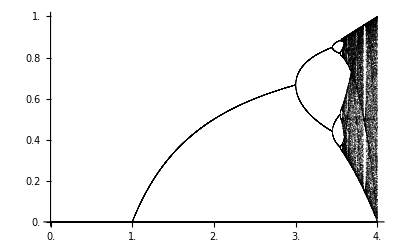

```mathematica
separazioni = %
```

```mathematica
Show[{separazioni,ParametricPlot[{#,y},{x,0,4},{y,0,1}]&/@positions2}]
```

-Graphics-

```mathematica
test[n_]:=(First/@data0⟦#⟧&/@(SequencePosition[data0,Table[{_,0},n],Overlaps->False]))
```

```mathematica
Manipulate[test[n],{n,15,30,1}]
```

{3.37998,3.44085,3.88812}